## Ancillary notebook to “Negative anomalous dimensions in N=4 SYM”

## Description

The aim of this notebook is to present a Mathematica code which can be used to find the eigensystem of the one-loop dilatation operator among scalar so(6) singlets in N=4 SYM. We extensively use the polynomial notation explained in Appendix E of the paper (We use x y instead of ϕ ϕ̄).

  We consider the mixing of length-six operators as an example. The code should work up to L=8 without difficulty, just by changing the value of “LL” which can be found in the section “Preliminary”. However, at larger L, the computation may take a long time, CPU workload and huge memory. Parallelization helps to reduce the computational time.
  
  The code should be executed from the top to bottom. 
  
  Only a very brief explanation is given at each computation. For more details of the Mathematica language, please refer to Wolfram Mathematica Tutorial Collection “Core Language” available from 
http://www.wolfram.com/learningcenter/tutorialcollection/CoreLanguage/

Comments on a green background are technical details of Mathematica implementation, which one does not have to understand.

## Preliminary

Define the operator length

```mathematica
LL=6;
```

Here are frequently used definitions, listed in alphabetical order

```mathematica
countLth[poly_]:=DeleteCases[Length/@Table[Join[Position[poly,Subscript[x, i]],Position[poly,Subscript[y, i]]],{i,Length@poly}],0];
countLxy[Subscript[x, i_],plis_]:=Length@Join[Position[plis,Subscript[x, i]],Position[plis,Subscript[y, i]]];
countLxy[Subscript[y, i_],plis_]:=countLxy[Subscript[x, i],plis];
countL0[plis_]:=Length@Join[Position[plis,Subscript[f, 0]],Position[plis,Subscript[fy, 0]],Position[plis,Subscript[p, 0]],Position[plis,Subscript[py, 0]],Position[plis,Subscript[x, 0]],Position[plis,Subscript[y, 0]]];

FS=FullSimplify;

gatherSpoly[spoly_]:=Total[Times@@@spoly];

indToMultiTrace[ind_]:=Module[
{Ltt=Table[Max[Flatten@ind[[u]]],{u,Length@ind}]},Product[trc[Table[Subscript[ϕ, p[u,v]],{v,Ltt[[u]]}]],{u,Length@Ltt}]/.Complement[Flatten@Table[If[ind[[j,k,l]]≠0,p[j,ind[[j,k,l]]]->i[k],0],{l,2},{k,1,Length@First@ind},{j,1,Length@ind}],{0}]/.i[x_]:>"i"<>ToString[x]];

indToPoly[ind_]:=Sum[Product[(Subscript[x, j])^ind[[j,k,1]](Subscript[y, j])^ind[[j,k,2]],{j,Length@ind}],{k,Length@First@ind}];

lengthSum[Ltt_List]:=Table[Sum[Ltt[[i1]],{i1,j1}],{j1,Length@Ltt}];

partitionLength[Lt_]:=Module[{fullpt=IntegerPartitions[Lt]},
Part[fullpt,Complement[Range[Length@fullpt],DeleteDuplicates@Position[fullpt,1][[All,1]]]]
];

polyToInd[poly_]:=Transpose[{D[List@@poly,x]/.{x->1,y->1},D[List@@poly,y]/.{x->1,y->1}}];
polyToInd[poly_,m_]:=Transpose/@Table[{D[List@@poly,Subscript[x, j]]/.Flatten@Table[{Subscript[x, i]->1,Subscript[y, i]->1},{i,m}],D[List@@poly,Subscript[y, j]]/.Flatten@Table[{Subscript[x, i]->1,Subscript[y, i]->1},{i,m}]},{j,m}];

polyToList[poly_]:=DeleteCases[Apply[List,Expand[poly+ωω]]/.ωω->0,0];polyToLog[poly_]:=polyToList[poly]/.{Subscript[x_, j1_]^k1_ Subscript[y_, j2_]^k2_->k1 Log[Subscript[x, j1]]+k2 Log[Subscript[y, j2]],Subscript[x_, j1_] Subscript[y_, j2_]^k2_-> Log[Subscript[x, j1]]+k2 Log[Subscript[y, j2]],Subscript[x_, j1_]^k1_ Subscript[y_, j2_]->k1 Log[Subscript[x, j1]]+ Log[Subscript[y, j2]],Subscript[x_, j1_] Subscript[y_, j2_]-> Log[Subscript[x, j1]]+Log[Subscript[y, j2]]};

powerOf[var_]:=D[var,First@Variables[var]]/.First@Variables[var]->1;

shiftInd[x_,y_,k_]={x->x^(1+k),y->y^(1+k),x^m_->x^(m+k),y^n_->y^(n+k)};
shiftInd[x_,y_,k_,L_]={x->x^(Mod[k,L]+1),y->y^(Mod[k,L]+1),x^m_->x^(Mod[m+k-1,L]+1),y^n_->y^(Mod[n+k-1,L]+1)};
shiftInd0[L0_,k0_,plis_]:=
plis/.{Subscript[f, 0]->(Subscript[f, 0])^(Mod[k0,L0]+1),(Subscript[f, 0])^m_->(Subscript[f, 0])^(Mod[m+k0-1,L0]+1),Subscript[fy, 0]->(Subscript[fy, 0])^(Mod[k0,L0]+1),(Subscript[fy, 0])^m_->(Subscript[fy, 0])^(Mod[m+k0-1,L0]+1),Subscript[p, 0]->(Subscript[p, 0])^(Mod[k0,L0]+1),(Subscript[p, 0])^m_->(Subscript[p, 0])^(Mod[m+k0-1,L0]+1),
Subscript[py, 0]->(Subscript[py, 0])^(Mod[k0,L0]+1),(Subscript[py, 0])^m_->(Subscript[py, 0])^(Mod[m+k0-1,L0]+1)};
shiftIndi[Subscript[x, i_],ki_,plis_]:=Module[{Li=countLxy[Subscript[x, i],plis]},
plis/.{Subscript[x, i]->Subscript[x, i]^(Mod[ki,Li]+1),Subscript[y, i]->Subscript[y, i]^(Mod[ki,Li]+1),Subscript[x, i]^m_->Subscript[x, i]^(Mod[m+ki-1,Li]+1),Subscript[y, i]^n_->Subscript[y, i]^(Mod[n+ki-1,Li]+1)}];
shiftIndi[Subscript[y, i_],ki_,plis_]:=shiftIndi[Subscript[x, i],ki,plis];

splitPoly[poly_]:=Exp[List@@@polyToLog[poly]];

SubFx[LL_]:=Table[Subscript[ϕ,ToString[i]<>ToString[x]]->Subscript[ϕ, ToExpression[ToString[i]<>ToString[x]]],{x,1,LL/2}]
```

## Generating multi-trace operators

### Definitions

taucomp[ ]  -- Take single-traces, generate equivalence class of cyclic rotation, split the single-trace
tauperm[ ] -- Generate equivalence class for Li=Lj interchange
multiRep[ ] -- Take the canonical so(2Nf) ordering, generate equivalence class for cyclic shift of each trace, and remove identical orbits

```mathematica
divider[lis_]:=Table[Take[Drop[lis,2j],2],{j,0,(Length@lis)/2-1}];
genEquivClass[lis_,Lt_]:=Table[Mod[lis+i,Lt]/. 0->Lt,{i,0,Lt-1}];
genEquivPoly[poly_,Lt_]:=Table[Expand[(x y)^i poly]/.Flatten@Table[{x^(Lt+i)->x^i,y^(Lt+i)->y^i},{i,1,Lt-1}],{i,0,Lt-1}];

splitter[poly_,Ltsum_List]:=poly/.Flatten@Table[{Piecewise[Join[{{x^i->(Subscript[x, τ[1]])^i,i≤Ltsum[[1]]}},Table[{x^i->(Subscript[x, τ[k]])^(i-Ltsum[[k-1]]),Ltsum[[k-1]]<i&&i≤Ltsum[[k]]},{k,2,Length@Ltsum}]]],Piecewise[Join[{{y^i->(Subscript[y, τ[1]])^i,i≤Ltsum[[1]]}},Table[{y^i->(Subscript[y, τ[k]])^(i-Ltsum[[k-1]]),Ltsum[[k-1]]<i&&i≤Ltsum[[k]]},{k,2,Length@Ltsum}]]]},{i,Last@Ltsum}];

genEquivPoly[poly_,LTab_List]:=Flatten[Fold[Table[#1,{id[#2],0,LTab[[#2]]-1}]&,
poly/.Flatten@Table[shiftInd[Subscript[x, l],Subscript[y, l],id[l]],{l,1,Length@LTab}],Range[Length@LTab]]]/.Flatten@Table[Table[{(Subscript[x, k])^(LTab[[k]]+j)->(Subscript[x, k])^j,(Subscript[y, k])^(LTab[[k]]+j)->(Subscript[y, k])^j},{j,1,LTab[[k]]-1}],{k,Length@LTab}];

tauperm[LTab_List]:=Module[{Ldup=Part[Tally@LTab,All,2]},
permlist[LTab]=Permutations@Range[#]&/@Ldup;
permlistLength[LTab]=Join[{0},lengthSum[Length/@permlist[LTab]]];
permIndices[LTab]=Map[Flatten,Tuples[
Table[permlist[LTab][[k]]+permlistLength[LTab][[k]],{k,Length@permlist[LTab]}]],1];
Table[Table[τ[i]->permIndices[LTab][[k,i]],{i,Length@LTab}],{k,Length@permIndices[LTab]}]
];

(* interchange x,y also before fixing tau-permutation to reduce the size of intermediate results *)
taucomp[LTab_List]:=Module[{Lt=Total[LTab]},
singClass[LTab]=genEquivPoly[#,Lt]&/@singlePoly[Lt];
tauPoly[LTab]=DeleteDuplicates@Flatten@splitter[#,lengthSum[LTab]]&@singClass[LTab];
DeleteDuplicates[tauPoly[LTab]/.{Subscript[x, τ[a_]]^c_ Subscript[y, τ[b_]]^d_/;c>d||(c==d&&a>b)->Subscript[x, τ[b]]^d Subscript[y, τ[a]]^c,
Subscript[x, τ[a_]]^c_ Subscript[y, τ[b_]]/;c>1->Subscript[x, τ[b]] Subscript[y, τ[a]]^c,Subscript[x, τ[a_]] Subscript[y, τ[b_]]/;a>b->Subscript[x, τ[b]] Subscript[y, τ[a]]}]
];

multiRep[LTab_List]:=Module[{multicomp=taucomp[LTab]/.tauperm[LTab]},
multicomp2[LTab]=genEquivPoly[#,LTab]&/@(DeleteDuplicates@Transpose[multicomp])/.{Subscript[x, a_]^c_ Subscript[y, b_]^d_/;c>d||(c==d&&a>b)->Subscript[x, b]^d Subscript[y, a]^c,Subscript[x, a_]^c_ Subscript[y, b_]/;c>1->Subscript[x, b] Subscript[y, a]^c,Subscript[x, a_] Subscript[y, b_]/;a>b->Subscript[x, b] Subscript[y, a]};
First/@DeleteDuplicates[Sort/@multicomp2[LTab]]
];
```

### Generating single-trace so(2Nf) singlets

```mathematica
pmlist=Join[{1},#]&/@Permutations@Table[i,{i,2,LL}];
pmlistOrd=divider/@Select[pmlist,(#[[3]]<#[[4]]&&#[[5]]<#[[6]])&];
pmcomp=DeleteDuplicates@Map[Sort,pmlistOrd,{1,2}];
```

```mathematica
Map[Sort,genEquivClass[#,LL]&/@pmcomp,{1,3}];
pmReps=Map[DeleteDuplicates,%,{0,1}];
```

```mathematica
singlePoly[LL]=Sort@Table[Sum[x^pmReps[[i,1,j,1]]y^pmReps[[i,1,j,2]],{j,LL/2}],{i,1,Length@pmReps}];
```

### Generating multi-trace so(2Nf) singlets

```mathematica
multiPoly[LL]=Table[multiRep[partitionLength[LL][[k]]],{k,2,Length@partitionLength[LL]}];
```

```mathematica
entirePoly[LL]=Join[List[singlePoly[LL]/.{x->Subscript[x, 1],y->Subscript[y, 1]}],multiPoly[LL]]
```

{{x_1 y_1^4+x_1^2 y_1^5+x_1^3 y_1^6,x_1 y_1^2+x_1^4 y_1^5+x_1^3 y_1^6,x_1 y_1^3+x_1^2 y_1^5+x_1^4 y_1^6,x_1 y_1^2+x_1^3 y_1^5+x_1^4 y_1^6,x_1 y_1^2+x_1^3 y_1^4+x_1^5 y_1^6},{x_2 y_1^2+x_2^2 y_1^3+x_1 y_1^4,x_1^2 y_1^3+x_1 y_1^4+x_2 y_2^2,x_2 y_1^2+x_1 y_1^3+x_2^2 y_1^4,x_1 y_1^3+x_1^2 y_1^4+x_2 y_2^2},{x_2 y_1^2+x_2^2 y_1^3+x_1 y_2^3,x_1^2 y_1^3+x_2 y_2^2+x_1 y_2^3,x_2 y_1^3+x_1^2 y_2^2+x_1 y_2^3},{x_2 y_1^2+x_3 y_2^2+x_1 y_3^2,x_3 y_1^2+x_2 y_2^2+x_1 y_3^2,x_1 y_1^2+x_2 y_2^2+x_3 y_3^2}}

### Results written in the operator form

```mathematica
entireTrc[LL]=Table[indToMultiTrace/@(polyToInd[#,Length@partitionLength[LL][[k]]]&/@entirePoly[LL][[k]]),{k,Length@entirePoly[LL]}]/.SubFx[LL];
OpBase=Flatten@entireTrc[LL]
baseNum=Length@OpBase
```

{trc[{ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i2,ϕ_i3,ϕ_i3}],trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}],trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}],trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}],trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}],trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}],trc[{ϕ_i2,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i1}],trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}],trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1}],trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i1}],trc[{ϕ_i1,ϕ_i1}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i3}]}

15

## Compute mixing matrix

### Definitions (using polynomial notation)

To each polynomial associated to a multi-trace operator, we assign an integer using subXYprime[ ].
If we have to deal with quite a lot of operators, we should assign well-separated prime numbers to {x_i,y_i}.
Empirically, separation should be around L/2.

```mathematica
separation=LL/2;
subXYprime[LL_]:=subXYprime[LL]=Flatten@Join[Table[{Subscript[x, i]->Prime[separation*i-1],Subscript[y, i]->Prime[separation*i]},{i,1,LL/2}]];
entireNum[LL]=entirePoly[LL]/.subXYprime[LL];
```

```mathematica
applyPy[spdilt_,spdilt2_,spList_]:=Module[{pyPos=Part[Position[spdilt,Subscript[py, 0]],All,3]},
Table[Flatten[Table[Table[Join[
{spdilt[[i0,1,pyPos[[i0]]]]},
{spList[[i,j,k]]},
{diltCoef[[i0]]},
{spdilt2[[i0,1]]},
{{spdilt[[i0,1,3-pyPos[[i0]]]],spList[[i,j,3-k]]}},
Drop[spList[[i]],{j}]],
{j,Length@spList[[i]]}],{i0,Length@spdilt},{k,1,2}],2],{i,Length@spList}]];
applyPyShuffle[dlt1_,dlt2_,polyList_]:=
applyPy[splitPoly/@dlt1,splitPoly/@dlt2,splitPoly/@polyList];
firstShift[fdTab_]:=Table[shiftInd0[4,4-powerOf@fdTab[[m,1]],#]&@
shiftIndi[First[Variables@fdTab[[m,2]]],-powerOf@fdTab[[m,2]],fdTab[[m]]],{m,Length@fdTab}];
firstJoin[plis_]:=Module[{isub=First@Variables[plis[[2]]]/.{Subscript[x, i_]->i,Subscript[y, i_]->i}},
plis[[3;;]]/.{Subscript[x, isub]->Subscript[x, 0]^4,Subscript[y, isub]->Subscript[y, 0]^4,Subscript[x, isub]^m_->Subscript[x, 0]^(m+3),Subscript[y, isub]^n_->Subscript[y, 0]^(n+3)}];
rotateP0[cplist_]:=Module[{pPos=Position[cplist,Subscript[p, 0]]},
Join[{cplist[[1]]},
{RotateRight[Extract[cplist,{pPos[[1,1]]}],1-pPos[[1,2]]]},
Drop[Drop[cplist,{pPos[[1,1]]}],{1}]]];
shiftP0[cplist_]:=Module[{pPow=1-powerOf[cplist[[2,1]]],L0=countL0[cplist]},
cplist/.{Subscript[f, 0]->(Subscript[f, 0])^(Mod[pPow,L0]+1),(Subscript[f, 0])^m_->(Subscript[f, 0])^(Mod[m+pPow-1,L0]+1),Subscript[fy, 0]->(Subscript[fy, 0])^(Mod[pPow,L0]+1),(Subscript[fy, 0])^m_->(Subscript[fy, 0])^(Mod[m+pPow-1,L0]+1),Subscript[p, 0]->(Subscript[p, 0])^(Mod[pPow,L0]+1),(Subscript[p, 0])^m_->(Subscript[p, 0])^(Mod[m+pPow-1,L0]+1),
Subscript[py, 0]->(Subscript[py, 0])^(Mod[pPow,L0]+1),(Subscript[py, 0])^m_->(Subscript[py, 0])^(Mod[m+pPow-1,L0]+1),Subscript[x, 0]->Subscript[x, 0]^(Mod[pPow,L0]+1),Subscript[y, 0]->Subscript[y, 0]^(Mod[pPow,L0]+1),Subscript[x, 0]^m_->Subscript[x, 0]^(Mod[m+pPow-1,L0]+1),Subscript[y, 0]^n_->Subscript[y, 0]^(Mod[n+pPow-1,L0]+1)}];
applyP[cnTab_]:=Flatten[Table[Join[
{Join[{cnTab[[i,2,1]],cnTab[[i,2,2]],Nf cnTab[[i,1]]},Drop[cnTab[[i]],2]]},Flatten[Table[Join[{cnTab[[i,2,1]],cnTab[[i,a,b]],cnTab[[i,1]]},
{{cnTab[[i,2,2]],cnTab[[i,a,3-b]]}},
Drop[Drop[cnTab[[i]],{a}],2]],{a,3,Length@cnTab[[i]]},{b,2}],{1,2}]],{i,Length@cnTab}],{1,2}];
removeFFy[cnTab_]:=Part[cnTab,Complement[Range[Length[cnTab]],
Part[Select[Join[Position[cnTab,Subscript[f, 0]],Position[cnTab,Subscript[fy, 0]]],Length[#]==3&],All,1]]];
secondShiftJoin[plis_]:=Module[{
isub=First@Variables[plis[[2]]]/.{Subscript[x, i_]->i,Subscript[y, i_]->i},
Lz=countL0[plis]},
Part[shiftIndi[First@Variables[plis[[2]]],1-powerOf@plis[[2]],plis],3;;]/.{(Subscript[f, 0])^m_->(Subscript[f, 0])^(m-1),(Subscript[fy, 0])^m_->(Subscript[fy, 0])^(m-1),Subscript[x, 0]^m_->Subscript[x, 0]^(m-1),Subscript[y, 0]^n_->Subscript[y, 0]^(n-1)}/.{Subscript[x, isub]->Subscript[x, 0]^(Lz-1),Subscript[y, isub]->Subscript[y, 0]^(Lz-1),Subscript[x, isub]^m_->Subscript[x, 0]^(m+Lz-2),Subscript[y, isub]^n_->Subscript[y, 0]^(n+Lz-2)}];
secondSplit[plis_]:=Module[{xyPow=powerOf@plis[[2]],
Lz=countL0[plis]},
Which[xyPow==2,Join[{Nc plis[[3]]},plis[[4;;]]/.{(Subscript[f, 0])^m_->(Subscript[f, 0])^(m-2),(Subscript[fy, 0])^m_->(Subscript[fy, 0])^(m-2),Subscript[x, 0]^m_->Subscript[x, 0]^(m-2),Subscript[y, 0]^n_->Subscript[y, 0]^(n-2)}],
xyPow==3||xyPow==Lz-1,Missing[],
3<xyPow<Lz-1,plis[[3;;]]/.Evaluate@Flatten[Join[Table[{(Subscript[f, 0])^m->(Subscript[f, 0])^(m-1),(Subscript[fy, 0])^m->(Subscript[fy, 0])^(m-1),Subscript[x, 0]^m->Subscript[x, 0]^(m-1),Subscript[y, 0]^m->Subscript[y, 0]^(m-1)},{m,2,xyPow}],
Table[{(Subscript[f, 0])^n->(Subscript[f, -1])^(n-xyPow),(Subscript[fy, 0])^n->(Subscript[fy, -1])^(n-xyPow),Subscript[x, 0]^n->Subscript[x, -1]^(n-xyPow),Subscript[y, 0]^n->Subscript[y, -1]^(n-xyPow)},{n,xyPow+1,Lz}]]],
xyPow==Lz,Join[{Nc plis[[3]]},plis[[4;;]]/.{(Subscript[f, 0])^m_->(Subscript[f, 0])^(m-1),(Subscript[fy, 0])^m_->(Subscript[fy, 0])^(m-1),Subscript[x, 0]^m_->Subscript[x, 0]^(m-1),Subscript[y, 0]^n_->Subscript[y, 0]^(n-1)}]]
];
secondDistribute[pTab_]:=Table[
If[Simplify[First@Variables[pTab[[k,2]]]/.{Subscript[x, i_]->i,Subscript[y, i_]->i}]==0,
secondSplit[pTab[[k]]],secondShiftJoin[pTab[[k]]]],{k,Length@pTab}];
rewriteXY[splis_]:=Join[{splis[[1]]},Table[{splis[[j,1]]/.{Subscript[x, i_]->Subscript[x, i],Subscript[x, i_]^a_->Subscript[x, i]^a,Subscript[y, i_]->Subscript[x, i],Subscript[y, i_]^a_->Subscript[x, i]^a,Subscript[f_, i_]->Subscript[x, i],Subscript[f_, i_]^a_->Subscript[x, i]^a},splis[[j,2]]/.{Subscript[x, i_]->Subscript[y, i],Subscript[x, i_]^a_->Subscript[y, i]^a,Subscript[y, i_]->Subscript[y, i],Subscript[y, i_]^a_->Subscript[y, i]^a,Subscript[f_, i_]->Subscript[y, i],Subscript[f_, i_]^a_->Subscript[y, i]^a}},{j,2,Length@splis}]];

arrangeInds[plis_]:=Module[{Idlis=Variables@(plis/.{Nc->1,Nf->1,y->x})/.Subscript[x, i_]->i,IdOrd},
IdOrd=Idlis[[Ordering[Length/@Table[Join[Position[plis,Subscript[x, i]],Position[plis,Subscript[y, i]]],{i,Idlis}],All,Greater]]];
plis/.Evaluate@Flatten[Join[Table[{Subscript[x, IdOrd[[i]]]->Subscript[x, τ[i]],Subscript[y, IdOrd[[i]]]->Subscript[y, τ[i]]},{i,Length@Idlis}]],1]
];

genEquivSplist[splis_]:=Module[{LTab=countLth[gatherSpoly@splis[[2;;]]/.{τ[i_]->i}],sptau},
sptau=splis/.tauperm[LTab];
Flatten[Fold[Table[#1,{id[#2],0,LTab[[#2]]-1}]&,
sptau/.Flatten@Table[shiftInd[Subscript[x, l],Subscript[y, l],id[l],LTab[[l]]],{l,1,Length@LTab}],Range[Length@LTab]],
Range[Length@LTab+1]]
];

listToPrime[lis_]:=Product[Prime[j]^lis[[j]],{j,Length@lis}];
sortTab[extTab_]:=Module[{orders=Ordering[#,All,listToPrime[countLth[#1]]<listToPrime[countLth[#2]]&]&/@extTab[[All,All,1]]},
Table[Table[extTab[[i,orders[[i,j]]]],{j,Length@orders[[i]]}],{i,Length@orders}]
];

sortTabDeep[extTab_]:=Module[{srTab=sortTab[extTab],lsTab,partBlock},
lsTab=Map[countLth,srTab,{3}];
partBlock=Part[Map[Tally,lsTab,{1,2}],All,All,2];
Table[Internal`PartitionRagged[srTab[[i]],partBlock[[i]]],{i,Length@srTab}]
];
interchangeXY[splist_]:={splist[[1]],gatherSpoly@splist[[2;;]]}/.{Subscript[x, a_]^c_ Subscript[y, b_]^d_/;c>d||(c==d&&a>b)->Subscript[x, b]^d Subscript[y, a]^c,Subscript[x, a_]^c_ Subscript[y, b_]/;c>1->Subscript[x, b] Subscript[y, a]^c,Subscript[x, a_] Subscript[y, b_]/;a>b->Subscript[x, b] Subscript[y, a]};

multiplyDuplicate[tlLis_]:={tlLis[[1,1]]tlLis[[2]],tlLis[[1,2;;]]};

numericTallied[polyTab_]:=Module[{numTlTab=Map[Tally,Map[DeleteDuplicates,Map[Flatten,polyTab,{3}],{3}]/.subXYprime[LL],{2}]},
Map[multiplyDuplicate,numTlTab,{3}]
];

compLengthSets[xtab_]:=Module[{idL=1,compL=List[],eidL,pmatch},
For[eidL=1,eidL≤Length@partitionLength[LL],eidL++,
pmatch[eidL]=Position[Table[
xtab[[idL,1,2,idCyc]]-entireNum[LL][[eidL]],
{eidOp,Length@entireNum[LL][[eidL]]},{idCyc,Length@xtab[[idL,1,2]]}],0];
If[pmatch[eidL]≠List[],
AppendTo[compL,eidL];idL++;If[idL>Length@xtab,Break[]]
];
];
compL
];
compMatchOp[xLis_,eLis_]:=Module[{eidO,xid,Omatch},
For[eidO=1,eidO≤Length@eLis,eidO++,
Omatch[eidO]=Position[Flatten@xLis[[2;;]]-eLis[[eidO]],0];
If[Length@Omatch[eidO]==1,xid=eidO;Break[],
If[Length@Omatch[eidO]>1,Print["Error: irregular match ",xLis];Break[]]];
If[eidO==Length@eLis,Print["Error: No match ",xLis];Break[]];
];
xid
];
compExtCoeff[xTab_,eLis_]:=Module[{posOp=Table[compMatchOp[xTab[[i]],eLis],{i,Length@xTab}]},
Table[Sum[xTab[[k,1]],{k,Flatten@Position[posOp,iv]}],{iv,Length@eLis}]
];
padCoeffZero[xTabs_,eTab_,CPL_]:=Module[{it=1,jL,tabCZ},
For[jL=1,jL≤Length@eTab,jL++,
If[MemberQ[CPL,jL],tabCZ[jL]=compExtCoeff[xTabs[[it]],Part[eTab,jL]];it++,
tabCZ[jL]=Table[0,{k,Length@eTab[[jL]]}]];
];
Table[tabCZ[j],{j,Length@eTab}]
];
```

### Actions of the one-loop dilatation

```mathematica
dilt1={Subscript[f, 0](Subscript[py, 0])^3,Subscript[f, 0](Subscript[py, 0])^4,(Subscript[p, 0])^2(Subscript[py, 0])^4,(Subscript[p, 0])^3(Subscript[py, 0])^4};
dilt2={(Subscript[fy, 0])^2(Subscript[p, 0])^4,(Subscript[fy, 0])^2(Subscript[p, 0])^3,Subscript[f, 0](Subscript[fy, 0])^3,Subscript[f, 0](Subscript[fy, 0])^2};
dilt=dilt1+dilt2;
diltCoef={-1/Nc,1/Nc,-1/(2 Nc),1/(2 Nc)};
diltP=diltCoef.P/@dilt;
```

First derivative by joining:
(1) Produce intermediate result (the shuffle) to keep simplicity of the code,
  coef (f^l py_0^k+F_0)(Σ_j x_j^a y_j^b)→List[{py_0^k,x_i^c,coef,sp[f^l y_i^d+Σ_(j≠i)x_j^a y_j^b+F_0]},{py_0^k,y_i^d,coef,sp[f^l x_i^c+Σ_(j≠i)x_j^a y_j^b+F_0]},(other i)]
where sp[ ] = splitPoly[ ]. Only dilt1 contains py, and the total action is dilt1+dilt2
(2) Count lengths, shift indices and generate new polynomials with coefficients
(3) Canonicalize the result

```mathematica
fdt=applyPyShuffle[dilt1,dilt2,Flatten@entirePoly[LL]];
fdt2=Map[firstJoin,firstShift/@fdt,{2}];
fdt3=Map[shiftP0,Map[rotateP0,fdt2,{2}],{2}];
```

Second derivative by joining or splitting:
(1) shuffle the list and remove the cases when p_0 acts on f_0,fy_0. Multiply a factor of Nf if p_0 acts on the pair
(2) compute joining or splitting. When p_0^d acts on x_i^a or y_j^b, it induces joining if i,j≠0  and splitting if i,j=0.
     Multiply a factor of Nc if the splitting takes place with a-d=±1,b-d=±1
     Returns Null for  a-d=±2,b-d=±2  corresponding to tr(Φ)=0
(3) Canonicalize the result
      replace f and fy; also for the pairs with two x’s or y’s
      rearrange subscripts to {τ[1],τ[2],...} in the order that  L_τ[1]≥L_τ[2]≥...

```mathematica
sdt=removeFFy/@applyP/@fdt3;
sdt2=DeleteMissing/@secondDistribute/@sdt;
sdt3=Map[arrangeInds,Map[rewriteXY,sdt2,{2}],{2}];
```

Rearrange the result in order to extract the matrix elements later:
(1) Generate equivalence class by tau-permutation and cyclic rotation;
(2) Create a new table deeper by one level, with the structure
        Table[[specify_dilatated_operator, specify_lengths, specify_each_term_of_dilatation_result, specify_equivalence_class]]
      We introduce inequality between length-sets in Young’s way;  val1<val2, {a, b, c, ...} →val=p[1]^a p[2]^b p[3]^c...
      where p[L]  is the L-th prime
(3) Replace the lists by polynomial in order to interchange x_i^a<->y_j^b  if a>b or a=b,i>j; delete duplicates and/or add them together
(4) Substitute integers for efficient comparison. Collect and tally identical terms produced by dilatation.

```mathematica
xdt=Map[genEquivSplist,sdt3,{2}];
xdt2=sortTabDeep[xdt];
xdt3=Map[DeleteDuplicates,Map[interchangeXY,xdt2,{4}],{3}];
xdt4=numericTallied[xdt3];
```

### Extract matrix elements (parallelize)

Compare and extract coefficients by a procedural code, keeping in mind that
i) some length sets  {L_1,L_2,...}  may be absent; check length-set to be compared
ii) stop search if something matches, exit loop with an error if nothing matches
iii) parallelize

```mathematica
tabCPL=compLengthSets/@xdt4;
```

```mathematica
LaunchKernels[];
DistributeDefinitions[entireNum,xdt4,tabCPL]
```

{entireNum,xdt4,tabCPL}

```mathematica
tabCoeff=Flatten/@ParallelTable[padCoeffZero[xdt4[[i]],entireNum[LL],tabCPL[[i]]],{i,Length@xdt4}];
```

### Summarize the result

DilM is the mixing matrix and OpBase if the operator basis. See Appendix A.1 for the notation.

```mathematica
DilM=tabCoeff
```

{{6,3,-6,0,0,(3 Nf)/Nc,3/Nc,-6/Nc,0,6/Nc-(3 Nf)/Nc,3/Nc,-6/Nc,0,0,0},{0,4+Nf,0,-4,2,2/Nc,2/Nc+(2 Nf)/Nc,-6/Nc,0,-4/Nc,3/Nc-Nf/Nc,2/Nc,0,0,0},{-2,1,6,-2,0,-6/Nc+Nf/Nc,1/Nc,4/Nc-(2 Nf)/Nc,2/Nc,-6/Nc,2/Nc+Nf/Nc,4/Nc-Nf/Nc,0,0,0},{0,-3/2,-2,6+Nf/2,0,-(2 Nf)/Nc,3/(2 Nc),-2/Nc,2/Nc+Nf/(2 Nc),2/Nc,1/Nc+Nf/Nc,-4/Nc,0,0,0},{0,3/2,0,-3,3+(3 Nf)/2,-6/Nc,15/(2 Nc)+(3 Nf)/(2 Nc),0,-3/Nc,0,0,0,0,0,0},{2/Nc,2/Nc+Nf/Nc,-4/Nc,-(2 Nf)/Nc,Nf/Nc,3+Nf/2,3/2,-2,0,0,0,0,-2/Nc,1/Nc+Nf/(2 Nc),1/(2 Nc)},{0,12/Nc,0,-24/Nc,12/Nc,0,3+2 Nf,0,-2,0,0,0,0,-2/Nc,1/Nc+Nf/Nc},{-4/Nc,-2/Nc,6/Nc-(2 Nf)/Nc,-2/Nc+(2 Nf)/Nc,2/Nc,-2,0,4,1,0,0,0,-Nf/Nc,1/Nc,0},{0,0,-24/Nc,24/Nc,0,0,-2,0,4+Nf,0,0,0,0,-(2 Nf)/Nc,2/Nc},{6/Nc-(3 Nf)/Nc,6/Nc,-12/Nc,6/Nc+(3 Nf)/Nc,-6/Nc,0,0,0,0,6,3,-6,0,0,0},{-4/Nc,-2/Nc-Nf/Nc,-4/Nc,4/Nc,6/Nc+Nf/Nc,0,0,0,0,0,2+Nf,0,0,0,0},{-6/Nc,(3 Nf)/Nc,12/Nc-(3 Nf)/Nc,-6/Nc,0,0,0,0,0,-6,3,6,0,0,0},{0,0,0,0,0,-6/Nc+(3 Nf)/Nc,3/Nc,6/Nc-(3 Nf)/Nc,-3/Nc,0,0,0,0,3,0},{0,0,0,0,0,24/Nc,-2/Nc+(2 Nf)/Nc,-24/Nc,2/Nc-(2 Nf)/Nc,0,0,0,0,Nf,2},{0,0,0,0,0,0,36/Nc,0,-36/Nc,0,0,0,0,0,3 Nf}}

```mathematica
OpBase
```

{trc[{ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i2,ϕ_i3}],trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i2,ϕ_i3,ϕ_i3}],trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}],trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}],trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}],trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}],trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}],trc[{ϕ_i2,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i1}],trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}],trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1}],trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i1}],trc[{ϕ_i1,ϕ_i1}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i3}]}

## Applications

### An eigensystem

```mathematica
esys=Chop@Eigensystem[N[Transpose@DilM/.Nf->6/.Nc->100]];
```

```mathematica
esys[[1]]
```

{18.012,15.7137,13.9867,11.9977,10.6776,9.45967,9.29545,7.99396,7.24412,6.45993,5.98997,2.76918,2.40599,-0.00601012,0}

```mathematica
esys[[2,-1]].OpBase
```

-0.446663 trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i1}]+0.893325 trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1}]+0.0496292 trc[{ϕ_i1,ϕ_i1}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i3}]

### A plot

Plot nonzero eigenvalues, which are sorted according to their real parts.

```mathematica
{Ncmax,Ncmin,Ncstep}={8,2,-1};Sort[#,Re[#1]>Re[#2]&]&/@(DeleteCases[#,0]&/@Table[Chop@Eigenvalues[N[DilM/.Nf->6]],{Nc,Ncmax,Ncmin,Ncstep}]);
tabev=Transpose[Table[Table[{Ncmax+Ncstep(i-1),Re[%[[i,j]]],Im[%[[i,j]]]},{j,Length[%[[i]]]}],{i,Length@%}]]
```

{{{8,19.6185,0},{7,20.0265,0},{6,20.6017,0},{5,21.4506,0},{4,22.788,0},{3,25.1221,0},{2,30.,0}},{{8,16.3587,0},{7,16.4392,0},{6,16.54,0},{5,16.6738,0},{4,16.865,0},{3,17.1429,0},{2,17.153,-0.909358}},{{8,12.8847,0},{7,12.8506,0},{6,12.8784,0},{5,13.0214,0},{4,13.3968,0},{3,14.3151,0},{2,17.153,0.909358}},{{8,11.3533,0},{7,11.2198,0},{6,11.2081,0},{5,11.3007,0},{4,11.5537,0},{3,12.1834,0},{2,13.6366,0}},{{8,10.8434,0},{7,10.7247,0},{6,10.6251,0},{5,10.8504,0},{4,11.1912,0},{3,11.7664,0},{2,13.,0}},{{8,10.2139,0},{7,10.3378,0},{6,10.2021,0},{5,9.81769,0},{4,9.93542,0},{3,9.80206,0},{2,8.84611,-0.574808}},{{8,9.42356,0},{7,9.50038,0},{6,9.60678,0},{5,9.33797,0},{4,8.0773,0},{3,7.91112,0},{2,8.84611,0.574808}},{{8,7.79211,0},{7,7.76184,0},{6,7.69237,0},{5,7.54111,0},{4,7.1496,0},{3,6.54598,0},{2,5.95689,-5.05105}},{{8,7.07741,0},{7,6.94964,0},{6,6.78123,0},{5,6.32546,0},{4,6.5,-1.65831},{3,6.45791,-3.37281},{2,5.95689,5.05105}},{{8,6.3083,0},{7,6.25956,0},{6,6.15148,0},{5,6.,0},{4,6.5,1.65831},{3,6.45791,3.37281},{2,5.19702,0}},{{8,4.76972,0},{7,4.55569,0},{6,4.60683,0},{5,5.45374,0},{4,5.33328,0},{3,4.09888,0},{2,2.62741,-1.63809}},{{8,3.61809,0},{7,3.81061,0},{6,3.79025,0},{5,3.29036,0},{4,2.69228,0},{3,2.95215,0},{2,2.62741,1.63809}},{{8,2.46931,0},{7,2.47117,0},{6,2.47174,0},{5,2.46221,0},{4,2.13684,0},{3,0.468897,0},{2,-2.84134,0}},{{8,-0.731065,0},{7,-0.90751,0},{6,-1.15617,0},{5,-1.52542,0},{4,-2.11945,0},{3,-3.22476,0},{2,-6.1591,0}}}

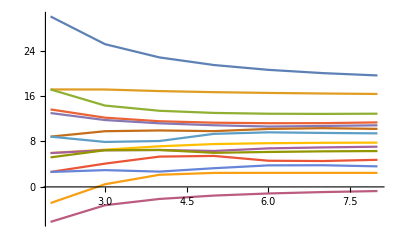

```mathematica
ListPlot[tabev[[All,All,;;2]],Joined->True,PlotRange->All]
```

## Appendix: L=10 results

This section explains how to read the L=10 results from the attached text file, which should be put on the same folder as this notebook.
Execute the section “Preliminary” to utilize this section.

```mathematica
LL=10;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"AncillaryL10Data.txt"
```

```mathematica
DilM=MixingMatrix[LL];
```

```mathematica
Tally/@Simplify[Dot[Transpose@Coefficient[DilM,Nc,0],#]&/@LargeNcZeroModes[LL]]
```

{{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}},{{0,469}}}

### Basis of operators at L=10

```mathematica
multiPoly[10]={{Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1]^5 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^5 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1]^4 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1]^6 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8,Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^6 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^5 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^6 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1]^4 Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8,Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1]^3 Subscript[y, 1]^8,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^5 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1]^4 Subscript[y, 1]^8,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 1]^7+Subscript[x, 1]^2 Subscript[y, 1]^8,Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 1]^4 Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1]^6 Subscript[y, 1]^7+Subscript[x, 1] Subscript[y, 1]^8+Subscript[x, 2] Subscript[y, 2]^2},{Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7,Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7,Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7,Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^5 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^4 Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^5 Subscript[y, 1]^7,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^5 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 1]^7+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^3 Subscript[y, 1]^7},{Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 1]^2 Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 1] Subscript[y, 2]^2,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2]^4 Subscript[y, 1]^6,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4},{Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3] Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1]^4 Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 1]^6,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 1]^6,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 1]^6+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2},{Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^3+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 1]^3 Subscript[y, 2]^3+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^3 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 2]^3 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^3 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^3 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^4 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 1]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^5,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^5},{Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2],Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2],Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2],Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^3 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^4 Subscript[y, 1]^5+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^3 Subscript[y, 1]^5+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2},{Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3] Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1]^2 Subscript[y, 2]^4,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 1]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^3 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^4,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 2]^4+Subscript[x, 3] Subscript[y, 3]^2},{Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 3] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 3]^3,Subscript[x, 3] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 3]^3,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^3+Subscript[x, 2]^2 Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 3]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 3],Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 3],Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 3]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 2] Subscript[y, 3]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 3]^3 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2]^2 Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 3]^3},{Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 3],Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 4]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 3]^2 Subscript[y, 1]^4+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3],Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 4]^2 Subscript[y, 1]^4+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 4]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 3],Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 3]^2 Subscript[y, 1]^3+Subscript[x, 4]^2 Subscript[y, 1]^4+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2,Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]+Subscript[x, 1] Subscript[y, 3]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 4]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2,Subscript[x, 1] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 1]^4+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2},{Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 3],Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 3] Subscript[y, 4]^2,Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 3] Subscript[y, 4]^2,Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2,Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 1]^2 Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 4] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 3] Subscript[y, 4]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 4] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3+Subscript[x, 1] Subscript[y, 3],Subscript[x, 3] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 2]+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3]^2 Subscript[y, 2]^3,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 4]^2 Subscript[y, 1]^3+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2,Subscript[x, 2] Subscript[y, 1]^3+Subscript[x, 1]^2 Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 2]^2 Subscript[y, 1]^3+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2,Subscript[x, 1]^2 Subscript[y, 1]^3+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 1] Subscript[y, 2]^3+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2},{Subscript[x, 5] Subscript[y, 1]^2+Subscript[x, 4] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]^2+Subscript[x, 1] Subscript[y, 5]^2,Subscript[x, 5] Subscript[y, 1]^2+Subscript[x, 3] Subscript[y, 2]^2+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]^2+Subscript[x, 1] Subscript[y, 5]^2,Subscript[x, 5] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 2] Subscript[y, 4]+Subscript[x, 1]^2 Subscript[y, 4]^2+Subscript[x, 1] Subscript[y, 5]^2,Subscript[x, 5] Subscript[y, 2]^2+Subscript[x, 2] Subscript[y, 3]+Subscript[x, 4] Subscript[y, 3]^2+Subscript[x, 1]^2 Subscript[y, 4]^2+Subscript[x, 1] Subscript[y, 5]^2,Subscript[x, 2] Subscript[y, 1]^2+Subscript[x, 5] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2+Subscript[x, 1] Subscript[y, 5]^2,Subscript[x, 5] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2+Subscript[x, 1] Subscript[y, 5]^2,Subscript[x, 1] Subscript[y, 1]^2+Subscript[x, 2] Subscript[y, 2]^2+Subscript[x, 3] Subscript[y, 3]^2+Subscript[x, 4] Subscript[y, 4]^2+Subscript[x, 5] Subscript[y, 5]^2}};
singlePoly[10]={x y^2+x^6 y^7+x^5 y^8+x^4 y^9+x^3 y^10,x y^2+x^5 y^7+x^6 y^8+x^4 y^9+x^3 y^10,x y^2+x^4 y^7+x^6 y^8+x^5 y^9+x^3 y^10,x y^2+x^5 y^7+x^4 y^8+x^6 y^9+x^3 y^10,x y^2+x^4 y^7+x^5 y^8+x^6 y^9+x^3 y^10,x y^2+x^4 y^6+x^5 y^8+x^7 y^9+x^3 y^10,x y^2+x^6 y^7+x^5 y^8+x^3 y^9+x^4 y^10,x y^2+x^5 y^7+x^6 y^8+x^3 y^9+x^4 y^10,x y^2+x^6 y^7+x^3 y^8+x^5 y^9+x^4 y^10,x y^3+x^2 y^7+x^6 y^8+x^5 y^9+x^4 y^10,x y^2+x^3 y^7+x^6 y^8+x^5 y^9+x^4 y^10,x y^2+x^3 y^6+x^7 y^8+x^5 y^9+x^4 y^10,x y^2+x^5 y^7+x^3 y^8+x^6 y^9+x^4 y^10,x y^3+x^2 y^7+x^5 y^8+x^6 y^9+x^4 y^10,x y^2+x^3 y^7+x^5 y^8+x^6 y^9+x^4 y^10,x y^2+x^3 y^5+x^7 y^8+x^6 y^9+x^4 y^10,x y^3+x^2 y^6+x^5 y^8+x^7 y^9+x^4 y^10,x y^2+x^3 y^6+x^5 y^8+x^7 y^9+x^4 y^10,x y^2+x^3 y^5+x^6 y^8+x^7 y^9+x^4 y^10,x y^2+x^3 y^6+x^5 y^7+x^8 y^9+x^4 y^10,x y^3+x^4 y^7+x^6 y^8+x^2 y^9+x^5 y^10,x y^2+x^6 y^7+x^4 y^8+x^3 y^9+x^5 y^10,x y^2+x^4 y^7+x^6 y^8+x^3 y^9+x^5 y^10,x y^6+x^2 y^7+x^3 y^8+x^4 y^9+x^5 y^10,x y^2+x^6 y^7+x^3 y^8+x^4 y^9+x^5 y^10,x y^3+x^2 y^7+x^6 y^8+x^4 y^9+x^5 y^10,x y^2+x^3 y^7+x^6 y^8+x^4 y^9+x^5 y^10,x y^2+x^3 y^6+x^7 y^8+x^4 y^9+x^5 y^10,x y^4+x^3 y^7+x^2 y^8+x^6 y^9+x^5 y^10,x y^3+x^4 y^7+x^2 y^8+x^6 y^9+x^5 y^10,x y^4+x^2 y^7+x^3 y^8+x^6 y^9+x^5 y^10,x y^2+x^4 y^7+x^3 y^8+x^6 y^9+x^5 y^10,x y^3+x^2 y^7+x^4 y^8+x^6 y^9+x^5 y^10,x y^2+x^3 y^7+x^4 y^8+x^6 y^9+x^5 y^10,x y^2+x^3 y^4+x^7 y^8+x^6 y^9+x^5 y^10,x y^2+x^4 y^6+x^3 y^8+x^7 y^9+x^5 y^10,x y^3+x^2 y^6+x^4 y^8+x^7 y^9+x^5 y^10,x y^2+x^3 y^6+x^4 y^8+x^7 y^9+x^5 y^10,x y^3+x^2 y^4+x^6 y^8+x^7 y^9+x^5 y^10,x y^2+x^3 y^4+x^6 y^8+x^7 y^9+x^5 y^10,x y^2+x^4 y^6+x^3 y^7+x^8 y^9+x^5 y^10,x y^2+x^3 y^6+x^4 y^7+x^8 y^9+x^5 y^10,x y^2+x^3 y^4+x^6 y^7+x^8 y^9+x^5 y^10,x y^3+x^4 y^7+x^5 y^8+x^2 y^9+x^6 y^10,x y^5+x^2 y^7+x^4 y^8+x^3 y^9+x^6 y^10,x y^2+x^5 y^7+x^4 y^8+x^3 y^9+x^6 y^10,x y^2+x^4 y^7+x^5 y^8+x^3 y^9+x^6 y^10,x y^5+x^2 y^7+x^3 y^8+x^4 y^9+x^6 y^10,x y^2+x^5 y^7+x^3 y^8+x^4 y^9+x^6 y^10,x y^3+x^2 y^7+x^5 y^8+x^4 y^9+x^6 y^10,x y^2+x^3 y^7+x^5 y^8+x^4 y^9+x^6 y^10,x y^2+x^3 y^5+x^7 y^8+x^4 y^9+x^6 y^10,x y^4+x^3 y^7+x^2 y^8+x^5 y^9+x^6 y^10,x y^3+x^4 y^7+x^2 y^8+x^5 y^9+x^6 y^10,x y^4+x^2 y^7+x^3 y^8+x^5 y^9+x^6 y^10,x y^2+x^4 y^7+x^3 y^8+x^5 y^9+x^6 y^10,x y^3+x^2 y^7+x^4 y^8+x^5 y^9+x^6 y^10,x y^2+x^3 y^7+x^4 y^8+x^5 y^9+x^6 y^10,x y^2+x^3 y^4+x^7 y^8+x^5 y^9+x^6 y^10,x y^3+x^2 y^5+x^4 y^8+x^7 y^9+x^6 y^10,x y^2+x^3 y^5+x^4 y^8+x^7 y^9+x^6 y^10,x y^3+x^2 y^4+x^5 y^8+x^7 y^9+x^6 y^10,x y^2+x^3 y^4+x^5 y^8+x^7 y^9+x^6 y^10,x y^2+x^4 y^5+x^3 y^7+x^8 y^9+x^6 y^10,x y^2+x^3 y^5+x^4 y^7+x^8 y^9+x^6 y^10,x y^2+x^3 y^4+x^5 y^7+x^8 y^9+x^6 y^10,x y^4+x^3 y^6+x^5 y^8+x^2 y^9+x^7 y^10,x y^4+x^2 y^6+x^5 y^8+x^3 y^9+x^7 y^10,x y^2+x^4 y^6+x^5 y^8+x^3 y^9+x^7 y^10,x y^3+x^2 y^6+x^5 y^8+x^4 y^9+x^7 y^10,x y^2+x^3 y^6+x^5 y^8+x^4 y^9+x^7 y^10,x y^3+x^2 y^5+x^6 y^8+x^4 y^9+x^7 y^10,x y^2+x^3 y^5+x^6 y^8+x^4 y^9+x^7 y^10,x y^4+x^2 y^6+x^3 y^8+x^5 y^9+x^7 y^10,x y^2+x^4 y^6+x^3 y^8+x^5 y^9+x^7 y^10,x y^3+x^2 y^6+x^4 y^8+x^5 y^9+x^7 y^10,x y^2+x^3 y^6+x^4 y^8+x^5 y^9+x^7 y^10,x y^3+x^2 y^4+x^6 y^8+x^5 y^9+x^7 y^10,x y^2+x^3 y^4+x^6 y^8+x^5 y^9+x^7 y^10,x y^4+x^2 y^5+x^3 y^8+x^6 y^9+x^7 y^10,x y^3+x^2 y^5+x^4 y^8+x^6 y^9+x^7 y^10,x y^2+x^3 y^5+x^4 y^8+x^6 y^9+x^7 y^10,x y^3+x^2 y^4+x^5 y^8+x^6 y^9+x^7 y^10,x y^2+x^3 y^4+x^5 y^8+x^6 y^9+x^7 y^10,x y^2+x^4 y^5+x^3 y^6+x^8 y^9+x^7 y^10,x y^2+x^3 y^5+x^4 y^6+x^8 y^9+x^7 y^10,x y^2+x^3 y^4+x^5 y^6+x^8 y^9+x^7 y^10,x y^2+x^5 y^6+x^4 y^7+x^3 y^9+x^8 y^10,x y^2+x^4 y^6+x^5 y^7+x^3 y^9+x^8 y^10,x y^2+x^5 y^6+x^3 y^7+x^4 y^9+x^8 y^10,x y^3+x^2 y^6+x^5 y^7+x^4 y^9+x^8 y^10,x y^2+x^3 y^6+x^5 y^7+x^4 y^9+x^8 y^10,x y^2+x^3 y^5+x^6 y^7+x^4 y^9+x^8 y^10,x y^2+x^4 y^6+x^3 y^7+x^5 y^9+x^8 y^10,x y^3+x^2 y^6+x^4 y^7+x^5 y^9+x^8 y^10,x y^2+x^3 y^6+x^4 y^7+x^5 y^9+x^8 y^10,x y^2+x^3 y^4+x^6 y^7+x^5 y^9+x^8 y^10,x y^3+x^2 y^5+x^4 y^7+x^6 y^9+x^8 y^10,x y^2+x^3 y^5+x^4 y^7+x^6 y^9+x^8 y^10,x y^3+x^2 y^4+x^5 y^7+x^6 y^9+x^8 y^10,x y^2+x^3 y^4+x^5 y^7+x^6 y^9+x^8 y^10,x y^2+x^4 y^5+x^3 y^6+x^7 y^9+x^8 y^10,x y^2+x^3 y^5+x^4 y^6+x^7 y^9+x^8 y^10,x y^2+x^3 y^4+x^5 y^6+x^7 y^9+x^8 y^10,x y^2+x^3 y^4+x^5 y^6+x^7 y^8+x^9 y^10}/.{x->Subscript[x, 1],y->Subscript[y, 1]};
entirePoly[LL]=Join[List[singlePoly[LL]],multiPoly[LL]];
entireTrc[LL]=Table[indToMultiTrace/@(polyToInd[#,Length@partitionLength[LL][[k]]]&/@entirePoly[LL][[k]]),{k,Length@entirePoly[LL]}]/.SubFx[LL];
OpBase=Flatten@entireTrc[LL];
baseNum=Length@OpBase
```

469

### Application

As an application, we present the explicit large Nc zero modes at L=10

```mathematica
Dot[OpBase,#]&/@LargeNcZeroModes[10]
```

{-40 trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i2}]-80 trc[{ϕ_i3,ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i2}]-80 trc[{ϕ_i4,ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i2}]+10 (4+Nf) trc[{ϕ_i4,ϕ_i4,ϕ_i2,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]-40 trc[{ϕ_i3,ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]-80 trc[{ϕ_i4,ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]+(-4-Nf) (6+Nf) trc[{ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+10 (4+Nf) trc[{ϕ_i3,ϕ_i2,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i4,ϕ_i1,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i4,ϕ_i1,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i2,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i4,ϕ_i1,ϕ_i2}]-40 trc[{ϕ_i4,ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]+10 (4+Nf) trc[{ϕ_i4,ϕ_i1,ϕ_i4,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i1,ϕ_i4,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i2,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i4,ϕ_i1,ϕ_i1}]+10 (4+Nf) trc[{ϕ_i3,ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i4,ϕ_i1,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i2,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i1,ϕ_i1,ϕ_i2}]-2 (4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i4,ϕ_i1,ϕ_i2}]+10 (4+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i1,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i2,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i1,ϕ_i2}]+10 (4+Nf) trc[{ϕ_i1,ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i2}]-5 (4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i2,ϕ_i4,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]-5 (4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]-5 (4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i4,ϕ_i2,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]-5 (4+Nf) (6+Nf) trc[{ϕ_i2,ϕ_i1,ϕ_i4,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]+10 (4+Nf) trc[{ϕ_i3,ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i2,ϕ_i1,ϕ_i2}]+20 (4+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i2,ϕ_i1,ϕ_i2}]+10 (4+Nf) trc[{ϕ_i2,ϕ_i2,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i3,ϕ_i1,ϕ_i1}]+(-4-Nf) (6+Nf) trc[{ϕ_i2,ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i3,ϕ_i1,ϕ_i2}],(-4-Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i4,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i3,ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i4,ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+4 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i4,ϕ_i4,ϕ_i2}] trc[{ϕ_i1,ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i3}]+4 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i4,ϕ_i4,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}]+(-4-Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i4,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i5,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i1,ϕ_i4}] trc[{ϕ_i5,ϕ_i5,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i5,ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+8 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i2,ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}]+8 trc[{ϕ_i4,ϕ_i1}] trc[{ϕ_i5,ϕ_i4,ϕ_i5}] trc[{ϕ_i2,ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}]+4 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i4,ϕ_i4,ϕ_i2}] trc[{ϕ_i3,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]+8 trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]+8 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i2,ϕ_i3}]+(-4-Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i4}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+8 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]+8 trc[{ϕ_i4,ϕ_i1}] trc[{ϕ_i5,ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i5,ϕ_i2}] trc[{ϕ_i4,ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]+(-4-Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i5,ϕ_i1}] trc[{ϕ_i4,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]-2 (4+Nf) trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i3}]-2 (4+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i3}]+(4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i5,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+(4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i5,ϕ_i2,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+(4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]+(4+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i4,ϕ_i3}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}]-2 (4+Nf) trc[{ϕ_i4,ϕ_i1}] trc[{ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]-2 (4+Nf) trc[{ϕ_i4,ϕ_i1}] trc[{ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}],4 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i4,ϕ_i3,ϕ_i4}]-4 (8+3 Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i3,ϕ_i3,ϕ_i2,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i1,ϕ_i2}]+(4+Nf)^2 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]-8 (8+3 Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i3,ϕ_i1}]-2 (8+3 Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i2,ϕ_i1,ϕ_i2}]-4 (8+3 Nf) trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i3,ϕ_i1,ϕ_i1}]+4 (4+Nf)^2 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i3,ϕ_i2,ϕ_i4}] trc[{ϕ_i4,ϕ_i3,ϕ_i1,ϕ_i2}]+(4+Nf)^2 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i3,ϕ_i1,ϕ_i2}]+16 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i3,ϕ_i4}]+16 trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i3,ϕ_i4}]+4 Nf^2 trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i2,ϕ_i5,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i5}]-4 Nf trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i4,ϕ_i5,ϕ_i4,ϕ_i5}]+2 Nf^2 trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i1,ϕ_i2}]+4 Nf^2 trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i1,ϕ_i2}]+4 Nf^2 trc[{ϕ_i1,ϕ_i4}] trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i2}]-Nf (4+Nf)^2 trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i1,ϕ_i4,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]+4 Nf (4+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i4,ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]+8 Nf (4+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]+8 Nf (4+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i4,ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]-2 Nf (4+Nf)^2 trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i4,ϕ_i2}]+8 Nf (4+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i4,ϕ_i2}]+2 Nf^2 trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i4,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i1,ϕ_i2}]+2 Nf^2 trc[{ϕ_i4,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i5,ϕ_i2,ϕ_i4,ϕ_i5}]-Nf (4+Nf)^2 trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i1,ϕ_i2}]-8 Nf trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i3,ϕ_i4,ϕ_i5}]-Nf (4+Nf)^2 trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2}]-Nf (4+Nf)^2 trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i2,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2}]+8 Nf (4+Nf) trc[{ϕ_i2,ϕ_i1}] trc[{ϕ_i3,ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2}]-8 Nf trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i5,ϕ_i4,ϕ_i4,ϕ_i5}]-16 Nf trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i5,ϕ_i4,ϕ_i4,ϕ_i5}],(32+8 Nf-4 Nf^2) trc[{ϕ_i2,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]-8 (2+Nf)^2 trc[{ϕ_i2,ϕ_i4,ϕ_i5}] trc[{ϕ_i4,ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]-8 (2+Nf)^2 trc[{ϕ_i5,ϕ_i2,ϕ_i4}] trc[{ϕ_i5,ϕ_i4,ϕ_i3}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]+(32+8 Nf-4 Nf^2) trc[{ϕ_i4,ϕ_i2,ϕ_i3}] trc[{ϕ_i5,ϕ_i4,ϕ_i5}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]+2 (-10+Nf) trc[{ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i3}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]+2 (2+Nf) trc[{ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]+2 (2+Nf) trc[{ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i3}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]-4 (2+Nf)^2 trc[{ϕ_i5,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i4,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i1,ϕ_i2}]+24 (2+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i4,ϕ_i1,ϕ_i2}]+4 (-10+Nf) trc[{ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]+4 (2+Nf) trc[{ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]+4 (2+Nf) trc[{ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]+(32+8 Nf-4 Nf^2) trc[{ϕ_i1,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]-4 (2+Nf)^2 trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i4,ϕ_i5,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]+2 (2+Nf)^2 (4+Nf) trc[{ϕ_i3,ϕ_i4,ϕ_i5}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i5,ϕ_i1,ϕ_i2}]+48 (2+Nf) trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i5,ϕ_i2}] trc[{ϕ_i4,ϕ_i1,ϕ_i1,ϕ_i2}]+(2+Nf)^2 (4+Nf) trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i2,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]+2 (2+Nf)^2 (4+Nf) trc[{ϕ_i1,ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i2,ϕ_i5}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]+(2+Nf)^2 (4+Nf) trc[{ϕ_i1,ϕ_i4,ϕ_i5}] trc[{ϕ_i4,ϕ_i2,ϕ_i3}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]-12 (8+6 Nf+Nf^2) trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i4,ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]-12 (8+6 Nf+Nf^2) trc[{ϕ_i1,ϕ_i5,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i4,ϕ_i1,ϕ_i2}],8 Nf (2+Nf) trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i1,ϕ_i2,ϕ_i3}]+(4-Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]-2 Nf trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]+2 trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i1,ϕ_i2}]+(8-2 Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]-4 Nf trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]+4 trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i1,ϕ_i1,ϕ_i2}]+Nf (2+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]+(-8+Nf) (2+Nf) trc[{ϕ_i1,ϕ_i4}] trc[{ϕ_i4,ϕ_i3}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]-4 (2+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i1,ϕ_i2,ϕ_i3}]+2 Nf (2+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}]+2 (-16-6 Nf+Nf^2) trc[{ϕ_i1,ϕ_i4}] trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}]-8 (2+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2,ϕ_i3}]-Nf (2+Nf) (4+Nf) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]-2 Nf (8+6 Nf+Nf^2) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i4,ϕ_i1,ϕ_i2,ϕ_i3}]+2 (8+6 Nf+Nf^2) trc[{ϕ_i1,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]+4 (8+6 Nf+Nf^2) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i3}] trc[{ϕ_i5,ϕ_i1,ϕ_i2,ϕ_i3}]+4 Nf (2+Nf) trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i4,ϕ_i3}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i2,ϕ_i1,ϕ_i2}],-2 (3+Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]+2 trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]-trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}]-trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}]+(6+Nf) trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i4,ϕ_i5}]-8 trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i4,ϕ_i5}]-2 (3+Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+2 trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+12 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+4 trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4}]+(6+Nf) trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2}]-8 trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2}],Nf (2+Nf)^2 trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]-2 (2+Nf)^2 trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]-2 (6+Nf) trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i1}]+(2+Nf)^2 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}]+(2+Nf)^2 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}]+8 (2+Nf)^2 trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i4,ϕ_i5}]+Nf (2+Nf)^2 trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]-2 (2+Nf)^2 trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]-8 Nf (2+Nf) trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+(32+4 Nf-2 Nf^2) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4}]+4 (6+Nf) trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4}]-32 (2+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2}],-6 Nf (2+Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]+12 (2+Nf) trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]+6 (6+Nf) trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i1}]+(-12-12 Nf-Nf^2) trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}]+(6+Nf) trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}]+(-12-12 Nf-Nf^2) trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}]+(6+Nf) trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}]+6 (-4+Nf^2) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i4,ϕ_i5}]-6 Nf (2+Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+12 (2+Nf) trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+48 Nf trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]-12 (6+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+12 (-2+Nf) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4}]-24 (-2+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2}],-Nf (2+Nf)^2 trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i1}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]+2 (2+Nf)^2 trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i3,ϕ_i4}] trc[{ϕ_i2,ϕ_i4,ϕ_i1}]+2 (6+Nf) trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i2,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i1}]+(6+Nf) trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i2,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i1}]-(2+Nf)^2 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}]-(2+Nf)^2 trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i1,ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i2,ϕ_i1}]+(-2+Nf) (2+Nf)^2 trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i5}] trc[{ϕ_i3,ϕ_i1,ϕ_i2}] trc[{ϕ_i3,ϕ_i4,ϕ_i5}]-Nf (2+Nf)^2 trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+2 (2+Nf)^2 trc[{ϕ_i3,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i1,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+8 Nf (2+Nf) trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]-2 (2+Nf) (6+Nf) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i5}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i1,ϕ_i2}]+2 (-4+Nf^2) trc[{ϕ_i3,ϕ_i5}] trc[{ϕ_i5,ϕ_i2}] trc[{ϕ_i1,ϕ_i1,ϕ_i2}] trc[{ϕ_i4,ϕ_i3,ϕ_i4}]-4 (-4+Nf^2) trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i5,ϕ_i4}] trc[{ϕ_i3,ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i1,ϕ_i2}],-6 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i4}] trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i1}]+2 Nf trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i1}]+8 trc[{ϕ_i1,ϕ_i2}] trc[{ϕ_i2,ϕ_i5}] trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i1}]+Nf^2 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i1}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i4}]-5 Nf trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i4}],30 Nf^2 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i4}] trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i1}]-10 Nf^3 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i4,ϕ_i2}] trc[{ϕ_i5,ϕ_i1}]-40 Nf trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i1}]-Nf^4 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i1}] trc[{ϕ_i2,ϕ_i3}] trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i4}]+5 Nf^3 trc[{ϕ_i1,ϕ_i5}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i1}] trc[{ϕ_i3,ϕ_i4}] trc[{ϕ_i5,ϕ_i4}]+16 trc[{ϕ_i1,ϕ_i1}] trc[{ϕ_i2,ϕ_i2}] trc[{ϕ_i3,ϕ_i3}] trc[{ϕ_i4,ϕ_i4}] trc[{ϕ_i5,ϕ_i5}]}